# Some connectivity based cluster validity indices

## 準備

```mathematica
Needs["HierarchicalClustering`"]
```

```mathematica
Needs["Combinatorica`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionaliy. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
(*SetDirectory["/Users/kouamano/gitsrc/ClusteringAdequation/test-data"]*)
```

```mathematica
SetDirectory["/Users/amanokou/gitsrc/ClusteringAdequation/test-data"]
```

/Users/amanokou/gitsrc/ClusteringAdequation/test-data

## 基本Programまとめ

minindexをつくる。
Input: dShortMat, Clusteringの結果(クラスタIDのリストのリスト).
output: メンバーID.

最終的に、z[k] = x[k,minindex]; z: medoid of cluster k, x: minindex-th member of cluster k、を求める。

距離行列から特定のクラスタに関する部分距離行列を抜き出す。

```mathematica
subDMat[dmat_,members_]:=Transpose[Transpose[dmat[[members]]][[members]]]
```

部分距離行列をもとに特定のクラスタのargminを求める。

```mathematica
argMinDMat[dmat_]:=Module[{sumList},
sumList=Map[Tr[#]&,dmat];
Position[sumList,Min[sumList]][[1]]
]
```

距離行列とクラスタリング結果から各クラスタのmedoidをもとめる。

```mathematica
findMedoidsParCL[dmat_,clusterResult_]:=Map[argMinDMat[subDMat[dmat,#]]&,clusterResult]
```

各クラスタのmedoid番号からもとのサンプル番号を求める。

```mathematica
(*orgIndexFromMedoidParCL[medoids_,clusterResult_]:=Inner[Part,clusterResult,medoids,List]*)
```

```mathematica
orgIndexFromMedoidParCL[clusterResult_,medoids_]:=Module[
{l,fmedoids},
l=Length[medoids];
fmedoids=Flatten[medoids];
Table[clusterResult[[i]][[medoids[[i]]]],{i,l}]
]
```

## Sample

```mathematica
sample={{1,1,2},
{2,1,4},
{3,3,5},
{4,5,4},
{3,2,5},
{1,3,1}
}
```

{{1,1,2},{2,1,4},{3,3,5},{4,5,4},{3,2,5},{1,3,1}}

## FindClusters Examples

```mathematica
fc=FindClusters[sample->Range[Length[sample]],3,Method->"Agglomerate"]
```

{{1,6},{2,3,5},{4}}

## DistanceMatrix

```mathematica
sampleDmat=Outer[EuclideanDistance,sample//N,sample,1]
```

{{0.,2.23607,4.12311,5.38516,3.74166,2.23607},{2.23607,0.,2.44949,4.47214,1.73205,3.74166},{4.12311,2.44949,0.,2.44949,1.,4.47214},{5.38516,4.47214,2.44949,0.,3.31662,4.69042},{3.74166,1.73205,1.,3.31662,0.,4.58258},{2.23607,3.74166,4.47214,4.69042,4.58258,0.}}

```mathematica
Export["sample.dmat",sampleDmat,"TSV"]
```

sample.dmat

RNG_d df = sample.dmat size = 6 > sample.RNGd

mk_d _short _mat loop = 6 dsize = 6 ef = sample.RNGd > sample.dsmat

```mathematica
sampleDSmat=Import["sample.dsmat","Table"]
```

{{2.23607,2.23607,2.23607,2.44949,2.23607,2.23607},{2.23607,1.73205,1.73205,2.44949,1.73205,2.23607},{2.23607,1.73205,1.,2.44949,1.,2.23607},{2.44949,2.44949,2.44949,2.44949,2.44949,2.44949},{2.23607,1.73205,1.,2.44949,1.,2.23607},{2.23607,2.23607,2.23607,2.44949,2.23607,2.23607}}

```mathematica
sampleDSmatZeroself=ReplacePart[sampleDSmat,{x_,x_}->0]
```

{{0,2.23607,2.23607,2.44949,2.23607,2.23607},{2.23607,0,1.73205,2.44949,1.73205,2.23607},{2.23607,1.73205,0,2.44949,1.,2.23607},{2.44949,2.44949,2.44949,0,2.44949,2.44949},{2.23607,1.73205,1.,2.44949,0,2.23607},{2.23607,2.23607,2.23607,2.44949,2.23607,0}}

```mathematica
subDMat[sampleDmat,fc[[2]]]
```

{{0.,2.44949,1.73205},{2.44949,0.,1.},{1.73205,1.,0.}}

```mathematica
argMinDMat[subDMat[sampleDmat,fc[[2]]]]
```

{3}

```mathematica
medoidsID=findMedoidsParCL[sampleDmat,fc]
```

{{1},{3},{1}}

```mathematica
medoidsID=findMedoidsParCL[sampleDmat,fc]
```

{{1},{3},{1}}

```mathematica
sampleMedoids=orgIndexFromMedoidParCL[fc,medoidsID]//Flatten
```

{1,5,4}

## cDB

cDB = Sum(R[i],{i,1,K}) / K   ; K:クラスタ数
R[i] = Max[{j,j≠i}]((S[i]+S[j])/d[i,j])   ; i:クラスタi, d[i,j]: ユークリッド距離行列
S[i] = Sum(dshort(x,z[i]),{x,x∈C[i]}) / n[i]   ; z[i]:medoid of cluster i, n[i]:number of cluster points.

### Program

距離行列とクラスタリング結果から各クラスタのmedoidをもとめる。

```mathematica
??findMedoidsParCL
```

Global`findMedoidsParCL

findMedoidsParCL[dmat_,clusterResult_]:=(argMinDMat[subDMat[dmat,#1]]&)/@clusterResult

各クラスタのmedoid番号からもとのサンプル番号を求める。

```mathematica
??orgIndexFromMedoidParCL
```

Global`orgIndexFromMedoidParCL

orgIndexFromMedoidParCL[clusterResult_,medoids_]:=Module[{l,fmedoids},l=Length[medoids];fmedoids=Flatten[medoids];Table[clusterResult⟦i⟧⟦medoids⟦i⟧⟧,{i,l}]]

```mathematica
s[dshortMatZeroself_,clMembers_,medoidIndex_]:=Tr[dshortMatZeroself[[medoidIndex,clMembers]]]/Length[clMembers]
```

```mathematica
r[edMat_,dshortMatZeroself_,cls_,medoids_,i_]:=Module[{js},
js=Drop[Range[Length[cls]],{i}];
Max[  Map[(s[dshortMatZeroself,cls[[i]],medoids[[i]]]+s[dshortMatZeroself,cls[[#]],medoids[[#]]])/edMat[[i,#]]&,js]  
]
]
```

```mathematica
cDB[edMat_,dshortMatZeroself_,cls_,medoids_]:=Tr[Table[r[edMat,dshortMatZeroself,cls,medoids,i],{i,Length[cls]}]]
```

### Examples

```mathematica
cDB[sampleDmat,sampleDSmatZeroself,fc,sampleMedoids]
```

2.18633

```mathematica
r[sampleDmat,sampleDSmatZeroself,fc,sampleMedoids,2]
```

0.90727

```mathematica
sampleDSmat[[1]]
```

{2.23607,2.23607,2.23607,2.44949,2.23607,2.23607}

```mathematica
sampleDSmat[[1,{1,4,6}]]
```

{2.23607,2.44949,2.23607}

s : i = 2

```mathematica
s[sampleDSmatZeroself,fc[[1]],sampleMedoids[[1]]]
```

1.11803

```mathematica
s[sampleDSmatZeroself,fc[[2]],sampleMedoids[[2]]]
```

0.910684

```mathematica
s[sampleDSmatZeroself,fc[[3]],sampleMedoids[[3]]]
```

0

## cDunn

cDunn = Min[i, 1, K] (Min[j,1,K ; j≠i]( d(C[i],C[j])/Max[k,1,K](delta(C[k])) ))
delta(C) = Max[x,y ∈ C](dshort(x,y)) ; diameter
d(C[i],C[j]) = Min[x∈C[i] , y∈C[j]](dshort(x,y))
C : クラスタ、K : クラスタ数

### Program

```mathematica
d[cl1_,cl2_,dshortMatZeroself_]:=Module[
{outer},
outer=Flatten[Outer[List,cl1,cl2,1],1];
Min[Map[dshortMatZeroself[[#[[1]],#[[2]]]]&,outer]]
]
```

```mathematica
delta[cl_,dshortMatZeroself_]:=Module[
{subset},
subset=Subsets[cl,{2}];
If[Length[subset]==0,0,Max[Map[dshortMatZeroself[[#[[1]],#[[2]]]]&,subset]]]
]
```

```mathematica
cDunn[cls_,dshortMatZeroself_]:=Module[
{numCls,maxdelta,subset},
numCls=Length[cls];
maxdelta=Max[Map[delta[#,dshortMatZeroself]&,cls]];
subset=Subsets[cls,{2}];
Min[Map[d[#[[1]],#[[2]],dshortMatZeroself]&,subset]]/maxdelta
]
```

### Examples

```mathematica
cDunn[fc,sampleDSmatZeroself]
```

1.

```mathematica
delta[fc[[3]],sampleDSmatZeroself]
```

0

```mathematica
fc[[2]]
```

{2,3,5}

```mathematica
d[fc[[2]],fc[[3]],sampleDSmatZeroself]
```

2.44949

```mathematica
fc[[1]]
```

{1,6}

```mathematica
fc[[2]]
```

{2,3,5}

## cGDunn

cGDunn = Min[s, 1, K](Min[t,1,K ; t≠s]( Gd(C[s],C[t])/Max[k,1,K](Gdelta(C[k])) )) .
Gdelta(S) = 2 (Sum[x∈S](dshort(x,z[S]))) / Length(S) ; z[S] : medoid of S ; S : クラスタ .
Gd(S,T) = 1 / (Length(S) Length(T)) Sum[x∈S,y∈T](dshort(x,y)) : S,T : クラスタ .

```mathematica
Gd[s_List,t_List,dshortMatZeroself_List]:=1/(Length[s] Length[t]) Tr[Flatten[Table[dshortMatZeroself[[s[[x]],t[[y]]]],{x,Length[s]},{y,Length[y]}]]]
```

```mathematica
Gdelta[s_List,medID_,dshortMatZeroself_List]:=2 Tr[Table[dshortMatZeroself[[s[[x]],medID]],{x,Length[s]}]]/ Length[s]
```

```mathematica
cGDunn[cls_List,dshortMatZeroself_List]:=Module[{medIDs,maxGdelta,subset},
medIDs=(orgIndexFromMedoidParCL[cls,findMedoidsParCL[dshortMatZeroself,cls]]//Flatten);
maxGdelta=Max[Table[Gdelta[cls[[i]],medIDs[[i]],dshortMatZeroself],{i,Length[cls]}]];
subset=Subsets[cls,{2}];
Min[Map[Gd[#[[1]],#[[2]],dshortMatZeroself]&,subset]]/maxGdelta
]
```

```mathematica
cGDunn[fc,sampleDSmatZeroself]
```

0.

## cPS

cPS=1/K∑_(i=1)^K 1/n[i]∑_(x∈S[i]) (dshort(x,z[i]))/dmin

dmin = Min[n,1,K; m,1,K; n≠m](dshort(z[n],z[m])) ; z[n]: medoid of cluster n .

## test

### cDunn

```mathematica
dsh={
{0,1,2,4,7},
{1,0,3,5,8},
{2,3,0,6,9},
{4,5,6,0,10},
{7,8,9,10,0}
}
```

{{0,1,2,4,7},{1,0,3,5,8},{2,3,0,6,9},{4,5,6,0,10},{7,8,9,10,0}}

```mathematica
cDunn[{{1,2},{3,4,5}},dsh]
```

1/5

```mathematica
d[{1,2},{3,4,5},dsh]
```

2

### 4_3

```mathematica
sphcsv=Import["/Users/amanokou/gitsrc/ClusteringAdequation/test-data/sph.csv","Table"];
```

```mathematica
sphcsvDrop=Transpose[Drop[Transpose[sphcsv],-1]];
```

```mathematica
Graphics3D[Map[Point[#]&,sphcsvDrop]]
```

-Graphics3D-

```mathematica
sphdmat=Outer[EuclideanDistance,sphcsvDrop,sphcsvDrop,1];
```

```mathematica
sphdmat//Dimensions
```

{400,400}

```mathematica
Export["sph.dmat",sphdmat,"Table"]
```

sph.dmat

```mathematica
Export["sphDrop.tsv",sphcsvDrop,Delimiters->" "]
```

sphDrop.tsv

```mathematica
sphcsvG=Gather[sphcsv,#1[[4]]==#2[[4]]&];
```

```mathematica
sphCl={Range[1,100],Range[101,200],Range[201,300],Range[301,400]};
```

```mathematica
sphCler[7]={Range[1,50],Range[51,100],Range[101,150],Range[151,200],Range[201,250],Range[251,300],Range[301,400]};
```

```mathematica
sphCler[3]={Range[1,150],Range[151,300],Range[301,400]};
```

```mathematica
sphCler[2]={Range[1,150],Range[151,400]};
```

```mathematica
sphDshort=Import["tmp","Table"];
```

```mathematica
sphDshortZeroself=ReplacePart[sphDshort,{x_,x_}->0];
```

```mathematica
Tr[sphDshortZeroself,List]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### cDB

```mathematica
??findMedoidsParCL
```

Global`findMedoidsParCL

findMedoidsParCL[dmat_,clusterResult_]:=(argMinDMat[subDMat[dmat,#1]]&)/@clusterResult

```mathematica
sphdmatMed=findMedoidsParCL[sphdmat,sphCl]
```

{{17},{27},{20},{35}}

```mathematica
sphdmatMeder[7]=findMedoidsParCL[sphdmat,sphCler[7]]
```

{{17},{48},{27},{25},{9},{6},{35}}

```mathematica
sphdmatMeder[3]=findMedoidsParCL[sphdmat,sphCler[3]]
```

{{83},{86},{35}}

```mathematica
??orgIndexFromMedoidParCL
```

Global`orgIndexFromMedoidParCL

orgIndexFromMedoidParCL[clusterResult_,medoids_]:=Module[{l,fmedoids},l=Length[medoids];fmedoids=Flatten[medoids];Table[clusterResult⟦i⟧⟦medoids⟦i⟧⟧,{i,l}]]

```mathematica
medoidssphCl=orgIndexFromMedoidParCL[sphCl,sphdmatMed]
```

{{17},{127},{220},{335}}

```mathematica
medoidssphCler[7]=orgIndexFromMedoidParCL[sphCler[7],sphdmatMeder[7]]
```

{{17},{98},{127},{175},{209},{256},{335}}

```mathematica
medoidssphCler[3]=orgIndexFromMedoidParCL[sphCler[3],sphdmatMeder[3]]
```

{{83},{236},{335}}

```mathematica
??cDB
```

Global`cDB

cDB[edMat_,dshortMatZeroself_,cls_,medoids_]:=Tr[Table[r[edMat,dshortMatZeroself,cls,medoids,i],{i,Length[cls]}]]

```mathematica
cDB[sphdmat,sphDshortZeroself,sphCl,medoidssphCl]
```

0.108221

```mathematica
cDB[sphdmat,sphDshortZeroself,sphCler[7],medoidssphCler[7]]
```

0.353692

```mathematica
cDB[sphdmat,sphDshortZeroself,sphCler[3],medoidssphCler[3]]
```

0.170121

#### cDunn

```mathematica
cDunn[sphCl,sphDshortZeroself]
```

2.93733

```mathematica
cDunn[sphCler[7],sphDshortZeroself]
```

0.0963575

```mathematica
cDunn[sphCler[3],sphDshortZeroself]
```

0.0625752

```mathematica
cDunn[sphCler[2],sphDshortZeroself]
```

0.0625752

### 5_2

```mathematica
Directory[]
```

/Users/amanokou/gitsrc/ClusteringAdequation/test-data

```mathematica
saha[5,2]=Import["/Users/amanokou/gitsrc/ClusteringAdequation/test-data/5_2.tbl","Table"];
```

```mathematica
sahaDrop[5,2]=Transpose[Drop[Transpose[saha[5,2]],-1]];
```

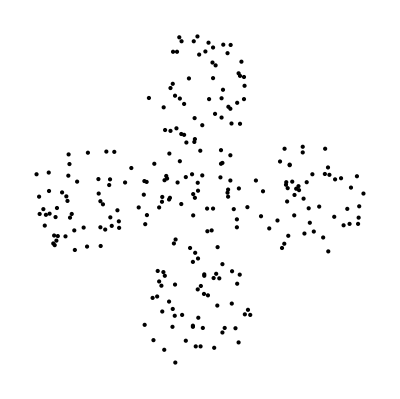

```mathematica
Graphics[Map[Point[#]&,sahaDrop[5,2]]]
```

```mathematica
(sahaEDist[5,2]=Outer[EuclideanDistance,saha[5,2],saha[5,2],1])//Dimensions
```

{250,250}

```mathematica
Export["saha_5_2.dmat",sahaEDist[5,2],"Table"]
```

saha_5_2.dmat

```mathematica
sahaDShort[5,2]=Import["saha_5_2.dshort","Table"];
```

```mathematica
sahaDShortZeroself[5,2]=ReplacePart[sahaDShort[5,2],{x_,x_}->0];
```

```mathematica
sahaCls[5,2]={Range[1,50],Range[51,100],Range[101,150],Range[151,200],Range[201,250]};
```

```mathematica
cDunn[sahaCls[5,2],sahaDShortZeroself[5,2]]
```

1.21695

階層クラスタリング

```mathematica
clAg=Agglomerate[sahaDrop[5,2]->Range[250],DistanceFunction->EuclideanDistance,Linkage->"Single"];
```

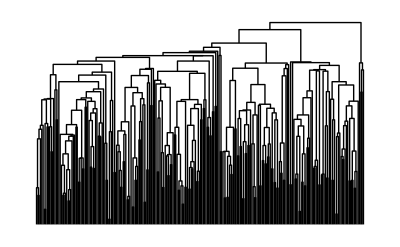

```mathematica
DendrogramPlot[clAg]
```

```mathematica
Map[ClusterFlatten[#]&,ClusterSplit[clAg,5]]
```

{{1,33,34,50,32,30,26,15,7,42,10,39,46,24,140,145,116,114,118,110,142,122,135,141,106,105,109,137,127,120,124,112,136,144,102,138,115,103,133,130,139,126,123,113,147,148,128,125,117,119,108,150,107,146,149,131,104,134,132,101,143,18,3,13,43,19,12,9,25,47,21,38,41,29,31,4,49,2,20,28,204,8,36,22,44,6,37,14,27,17,244,227,247,238,228,239,217,248,216,246,230,221,218,208,201,214,209,203,231,222,211,226,242,235,229,224,213,233,232,210,223,225,245,240,236,234,241,249,220,243,237,250,212,206,202,215,129,111,121},{219,207,205},{165,193,157,176,158,189,164,199,16,173,190,196,191,198,162,155,151,152,188,163,154,174,179,181,197,195,177,182,156,183,160,171,161,166,169,153,167,186,170,184,172,159,178,168,187,180,175,200,194,192,185},{48,5,23,96,60,56,90,81,73,71,63,65,52,68,62,54,78,84,97,77,11,35,45,40,64,79,51,100,58,74,76,67,61,88,92,75,91,66,85,57,83,98,80,89,53,55,59,72,86,95,70,93,94},{69,87,82,99}}

```mathematica
slRes[3]=FindClusters[sahaDrop[5,2]->Range[250],5,Method->"Agglomerate"]
```

{{1,2,3,4,6,7,8,9,10,12,13,14,15,17,18,19,20,21,22,24,25,26,27,28,29,30,31,32,33,34,36,37,38,39,41,42,43,44,46,47,49,50,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,201,202,203,204,206,208,209,210,211,212,213,214,215,216,217,218,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250},{5,11,23,35,40,45,48,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,70,71,72,73,74,75,76,77,78,79,80,81,83,84,85,86,88,89,90,91,92,93,94,95,96,97,98,100},{16,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200},{69,82,87,99},{205,207,219}}

```mathematica
cDunn[slRes[3],sahaDShortZeroself[5,2]]
```

0.331548

```mathematica
MinimumSpanningTree
```